# PreModule

## Temperature

```mathematica
Rbpress[T_]:=
(*
Calculates the vapor pressure of Na depending on the temprerature of the cell.;
Input variable: T:temperature[C];
Output variable: p=Na pressure[torr];
Formulas obtained from "Sodium D Line Data" by Daniel A.Steck;
http://steck.us/alkalidata
*)

Module[{T1,p,k,c,MRb,w0,Nat,dopp},
T1=T+273.15;
(*If[T1<39.31+273.15,p=10^(-94.04826-1961.258/T1-0.03771687*T1+42.57526*Log[10,T1])
,p=10^(15.88253-4529.635/T1+0.00058663*T1-2.99138*Log[10,T1])
];*)
p= If[T1<312.5,10^(9.863-4215/T1),10^(9.318-4040/T1)];(*Unit is in Pa*)
k=1.3806503 10^-23; (*Boltzman's contstant[J/K]*)
c=2.99792458 10^8;(*Speed of light[m/s]*)
MRb=1.409993119 10^-25;(*Rb 85 atomic mass[kg]*)
(*w0=2Pi 377.107385*10^12;(*Transition frequency for 85Rb D1 line*)
dopp=w0/c*Sqrt[2 k*T1/MRb];*)
w0=2Pi 377.107385*10^12;
dopp=2 w0/c*Sqrt[2 Log[2 ]k*T1/MRb]/(2Pi);
Nat=p/(k*T1); (*units in m^-3*)

{Nat,dopp,p,Sqrt[3k*T1/MRb]}
]
```

## 3Level

```mathematica
χ3a=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ Ωc^2) ℏ);  
χ3e=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ Ωc^2) ℏ);
```

```mathematica
s3a=χ3a/.Δ->Δ+wc v/c/.δ->δ;
s3a=s3a/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s3e=χ3e/.Δ->Δ+wc v/c/.δ->δ;
s3e=s3e/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α1∉Reals,Integrate[(ⅇ^(-v^2/u^2))/(v+α1),{v,-∞,∞}]]//FullSimplify*)
```

```mathematica
Dopp3[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=num/CoefficientList[den,v][[2]]//FullSimplify;

α1=CoefficientList[den,v][[1]]/CoefficientList[den,v][[2]]//FullSimplify;
Int=A ⅇ^(-α1^2/u^2) (ⅈ π Erfc[I α1/u])
(*Int=A (π 2 /Sqrt[π] DawsonF[α1/u]-Log[-1/α1] ⅇ^(-α1^2/u^2)-Log[α1] ⅇ^(-α1^2/u^2))//Simplify*)
]
```

## 4Level

```mathematica
χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);
```

```mathematica
s42=χ42/.Δ->Δ+wc v/c/.δ->δ;
s42=s42/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s32=χ32/.Δ->Δ+wc v/c/.δ->δ;
s32=s32/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s23=χ23/.Δ->Δ+wc v/c/.δ->δ;
s23=s23/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
s24=χ24/.Δ->Δ+wc v/c/.δ->δ;
s24=s24/.Nat-> Nat/(u Sqrt[Pi])Exp[-v^2/u^2]//ExpandAll//FullSimplify;
```

```mathematica
(*Assuming[u> 0&&u∈Reals&&α1∉Reals&&α2∉Reals,Integrate[((v +Zα)ⅇ^(-v^2/u^2))/((v-α1)(v-α2)),{v,-∞,∞}]]*)
```

```mathematica
Dopp[χ_]:=Module[{num,den,A,ans,α1,α2,Zα,Int},
num=Numerator[χ];
den=Denominator[χ] ⅇ^(-v^2/u^2);
A=CoefficientList[num,v][[2]]/CoefficientList[den,v][[3]];
ans=Solve[den/CoefficientList[den,v][[3]]==0,v];
α1=ans[[1,1,2]]//FullSimplify;
α2=ans[[2,1,2]]//FullSimplify;
Zα= CoefficientList[num,v][[1]]/CoefficientList[num,v][[2]]//FullSimplify;
Int=A(-ⅇ^(-α1^2/u^2) (Zα+α1) (-I π (Erfc[-I α1/u]))+ⅇ^(-α2^2/u^2) (Zα+α2) (-I π (Erfc[-I α2/u])))/(α1-α2)
(*Int=A(- (Zα+α1) (π 2 /Sqrt[π] DawsonF[α1/u]-ⅈ π ⅇ^(-α1^2/u^2))+ (Zα+α2) (π 2 /Sqrt[π] DawsonF[α2/u]-ⅈ π ⅇ^(-α2^2/u^2)))/(α1-α2)*)

]
```

## Define function

```mathematica
sd32[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s32]];
(*sd23[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d32_]:=Evaluate[Dopp[s23]];
sd24[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s24]];*)
sd42[wc_,γ21_,γ42_,γ32_,δ_,Δ_,omegac1_,c_,ℏ_,e0_,u_,Nat_,w43_,d42_]:=Evaluate[Dopp[s42]];
sd3a[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3a]];
sd3e[wc_,γ21_,γ32_,δ_,Δ_,Ωc_,c_,ℏ_,e0_,u_,Nat_,d32_]:=Evaluate[Dopp3[s3e]];
```

```mathematica
Ome[P_,diam_]:=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)])/.{ℏ-> 1.0546 10^-34,e0->8.8542 10^-12,c-> 2.9979 10^8,d31-> Sqrt[2/27]*2.537717 10^-29}
```

```mathematica
Ome[10/1000,1.4/1000]
Ome[20/1000,1.4/1000]
Ome[50/1000,1.4/1000]
Ome[100/1000,1.4/1000]
```

1.02455×10^8

1.44893×10^8

2.29096×10^8

3.23991×10^8

```mathematica
Lev3Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ24]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[χ42]]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4Test[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
},
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]
]
]
```

```mathematica
Lev4DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41},
d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]
]
]
```

```mathematica
Lev3DoppTest[T_,P_,diam_,gam_,delt_,ab_,kk_:0] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,d31,d41},

d=Range[-2,2,0.02]*10^9;
Δ=2Pi d;(*Raman detuning*)
Nat=Rbpress[T][[1]];
δ=2Pi delt;
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
{Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Exp[-2Pi*0.0254/(2wcn)Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
},
Transpose[{If[kk==0,d/10^9,(d/10^9+kk)],
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
]
]
```

```mathematica
Lev3Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(4 d42^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ+w43)-ⅈ omegac2^2) ℏ);   
χ24=(4 d42^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ+w43)+ⅈ omegac2^2) ℏ);   
χ32=(4 d32^2 Nat (γ21+ⅈ δ))/(e0 (4 (γ21+ⅈ δ) (-ⅈ γ32+δ+Δ)-ⅈ omegac1^2) ℏ);   
χ23=(4 d32^2 Nat (γ21-ⅈ δ))/(e0 (4 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)+ⅈ omegac1^2) ℏ); 

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[χ42]+Im[χ32])}],
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.6,0.4,0.0013]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4Testsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,d31,d41,Δ2},
d=Range[-0.6,0.4,0.001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 
omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

χ42=(d42^2 Nat ((4 √5-5 √14) omegac1^2+16 √5 (γ21+ⅈ δ) (γ32+ⅈ (δ+Δ))))/(2 √5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ32=-(d32^2 Nat ((-35+2 √70) omegac1^2+40 (-ⅈ γ21+δ) (w43-ⅈ γ42+δ+Δ)))/(5 e0 (omegac1^2 (2 w43-7 ⅈ γ32-2 ⅈ γ42+9 δ+9 Δ)+8 (γ21+ⅈ δ) (w43-ⅈ γ42+δ+Δ) (γ32+ⅈ (δ+Δ))) ℏ);
χ24=(d42^2 Nat (ⅈ (4 √5-5 √14) omegac1^2+16 √5 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ)))/(2 √5 e0 (8 (γ21-ⅈ δ) (ⅈ γ32+δ+Δ) (w43+ⅈ γ42+δ+Δ)+ⅈ omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)) ℏ);
χ23=(d32^2 Nat ((35 √2-4 √35) omegac1^2-40 ⅈ √2 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ)))/(5 √2 e0 (omegac1^2 (2 w43+7 ⅈ γ32+2 ⅈ γ42+9 δ+9 Δ)+8 (γ21-ⅈ δ) (w43+ⅈ γ42+δ+Δ) (γ32-ⅈ (δ+Δ))) ℏ);

If[ab==0,
(*{Transpose[{d/10^9,Im[χ24]}],
Transpose[{d/10^9,Im[χ42]}],
Transpose[{d/10^9,Im[χ23]}],
Transpose[{d/10^9,Im[χ32]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}],
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42]+Im[χ32])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
(Im[χ32])
}],
Transpose[{d/10^9,
(Im[χ42])
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ32])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[χ42])]
}]}
]]
]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.3,0.4,0.0007]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
{Transpose[{d/10^9,
(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])
}],Transpose[{d/10^9,
(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])
}],Transpose[{d/10^9,
(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]+Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])
}]}

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
zz[u_,Ohm_]:=c/(u wp)(γ21-I Δ+(Ohm^2/4)/(γ31-I δ))
```

```mathematica
(Exp[zz[u,Ohm]^2](1-Erf[zz[u,Ohm]]))/(Exp[zz[u,0]^2](1-Erf[zz[u,0]]))
```

(ⅇ^(-(c^2 (γ21-ⅈ Δ)^2)/(u^2 wp^2)+(c^2 (γ21+Ohm^2/(4 (γ31-ⅈ δ))-ⅈ Δ)^2)/(u^2 wp^2)) (1-Erf[(c (γ21+Ohm^2/(4 (γ31-ⅈ δ))-ⅈ Δ))/(u wp)]))/(1-Erf[(c (γ21-ⅈ Δ))/(u wp)])

```mathematica
Clear[Ohm]
```

```mathematica
1-(Exp[zz[u,Ohm]^2](1-Erf[zz[u,Ohm]]))/(Exp[zz[u,0]^2](1-Erf[zz[u,0]]))/.{c->1,γ21->0,δ->0,wp->1,Δ->0,γ31->γ31}//ExpandAll//Simplify
```

1-ⅇ^(Ohm^4/(16 u^2 γ31^2))+ⅇ^(Ohm^4/(16 u^2 γ31^2)) Erf[Ohm^2/(4 u γ31)]

```mathematica
Limit[(1-ⅇ^(Ohm^4/(16 u^2 γ31^2))+ⅇ^(Ohm^4/(16 u^2 γ31^2)) Erf[Ohm^2/(4 u γ31)])/.{Ohm->1,u->x},γ31->0]
```

Limit[1-ⅇ^(1/(16 x^2 γ31^2))+ⅇ^(1/(16 x^2 γ31^2)) Erf[1/(4 x γ31)],γ31→0]

```mathematica
Limit[Erf[1/(4 x)],x->0]
```

1

```mathematica
Ohm=5;
Manipulate[1-N[(Exp[zz[u,Ohm]^2](1-Erf[zz[u,Ohm]]))/(Exp[zz[u,0]^2](1-Erf[zz[u,0]]))/.{c->1,γ21->1,δ->0,wp->1,Δ->0,γ31->γ}],{γ,0,1},{u,1,100}]
```

```mathematica
x
```

x

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.1,0.1,0.00005]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(210.923*10^6) +2Pi(150.659*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Manipulate[sd3a[1,γ21,1,0,0,10,1,1,1,u,Nat,1]/sd3a[1,γ21,1,0,0,0,1,1,1,u,Nat,1]//Chop,{Nat,1,10},{{γ21,0.1},0,1}]
```

$Aborted

```mathematica
p=15.865;
Manipulate[
GraphicsRow[{ListPlot[{Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0],Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0]},ImageSize->500,PlotRange->All,Axes->False,Frame->True,ImageSize->Large,Joined->True,PlotLegends->Placed[{Im[χEIT],Im[χAbs]},{0.8,0.5}]],ListPlot[{1-Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0][[All,2]]/Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0][[All,2]]},PlotRange->{0,1},PlotLegends->Placed[{"1-Im[χEIT]/Im[χAbs]"},{0.8,0.5}],Axes->False,Frame->True,ImageSize->Large,Joined->True]},ImageSize->1000],{T,-200,300},{{γ,0.01},0,1}]
```

# Figure

## Module

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.003,0.003,0.00004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 



{Transpose[{d/10^9,(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])}],Transpose[{d/10^9,(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])}],Transpose[{d/10^9,(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])}]}


]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.003,0.003,0.00004]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

```mathematica
Lev4DoppTestscp[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


{Transpose[{d/10^9,(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])}],Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],Transpose[{d/10^9,(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])}]}


]
```

```mathematica
Lev3DoppTestscp[T_,P_,diam_,gam_,delt_,ab_,w_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

```mathematica
p=15.865;
Manipulate[
ListPlot[{Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0][[1]],Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0][[2]],Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0][[3]],Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0][[3]]},PlotRange->All,Axes->False,Frame->True,ImageSize->Large,Joined->True,PlotStyle-> {{Red,Dashed},{Blue,Dashed},Black,Gray},PlotLegends->{"Doppleter Four level 32","Doppleter Four level 41","Doppleter Four level together","No power"}],{{T,50},-200,300},{{γ, 0.01*5},0,1}]
```

```mathematica
p=15.865;
Manipulate[
ListPlot[{
Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6][[1]],
Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6][[2]],
Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6][[3]],
Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6][[3]]},PlotRange->{-0.00001,0.00003},PlotStyle->{{Red,Dashed},{Blue,Dashed},Black,Gray},Axes->False,Frame->True,ImageSize->Large,Joined->True,Epilog->{Line[{{-1,3*10^-6},{1,3*10^-6}}],Line[{{-1,0},{1,0}}]}],{{T,50},-200,300},{{γ, 0.01*5},0,1},{{i,0.0001},0,5}]
```

## TvS vs Temperatue

γ=0MHZ

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=0;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4[T]={};Tvw3[T]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4[T]=Append[Tvw4[T],{i,1-EIT1/ABS1}];
Tvw3[T]=Append[Tvw3[T],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{T,{400,300,200,100,0}}]
]
```

400

$Aborted

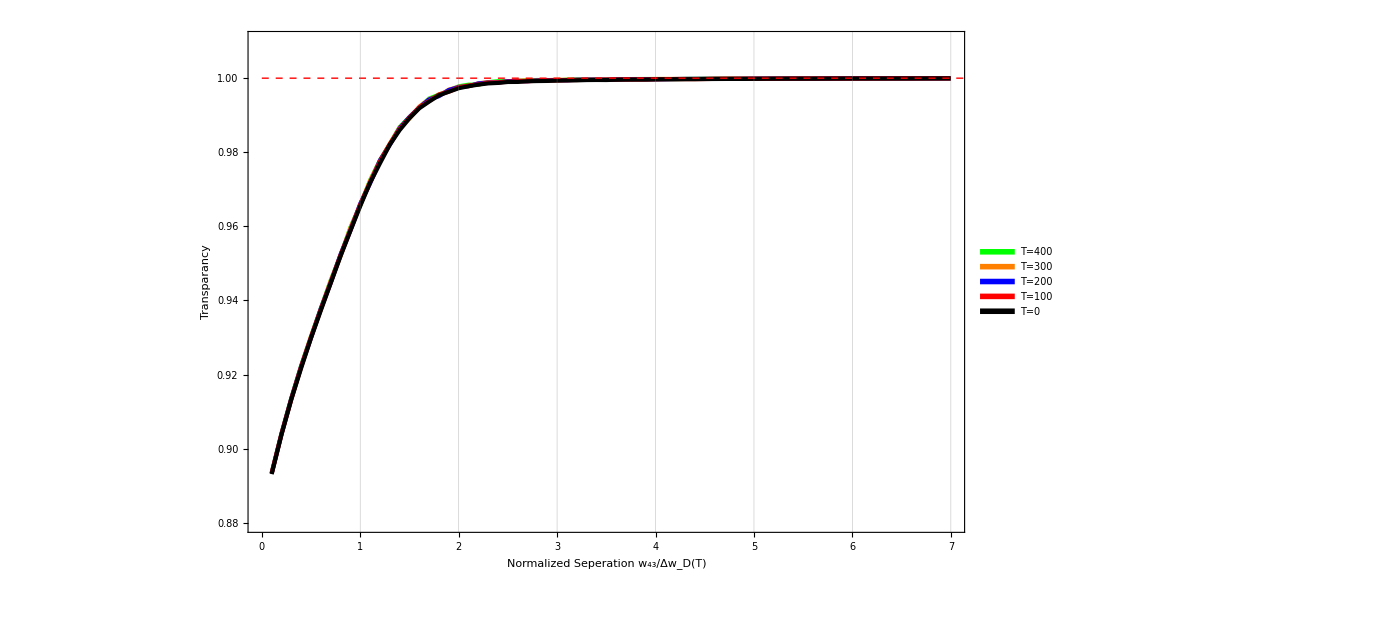

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMMp0=ListPlot[Table[Tvw4[T],{T,{400,300,200,100,0}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0.88,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\Final-Paper Figure"]
Export["Figure9Combinedf1.eps",MMMp0]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\Final-Paper Figure

Figure9Combinedf1.eps

γ=0.5 MHZ

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=0.5;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4γ5[T]={};Tvw3γ5[T]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4γ5[T]=Append[Tvw4γ5[T],{i,1-EIT1/ABS1}];
Tvw3γ5[T]=Append[Tvw3γ5[T],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{T,{400,300,200,100,0,-100,-200,-250}}]
]
```

400

300

200

100

0

-100

-200

-250

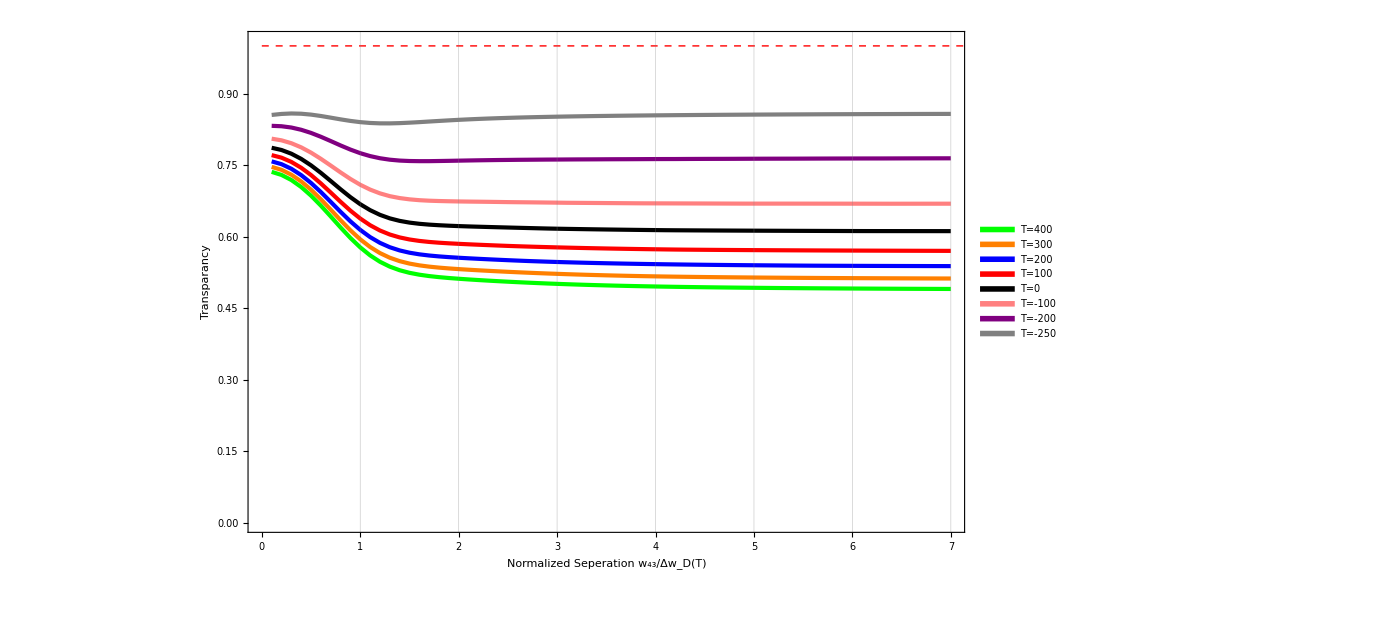

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw4γ5[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

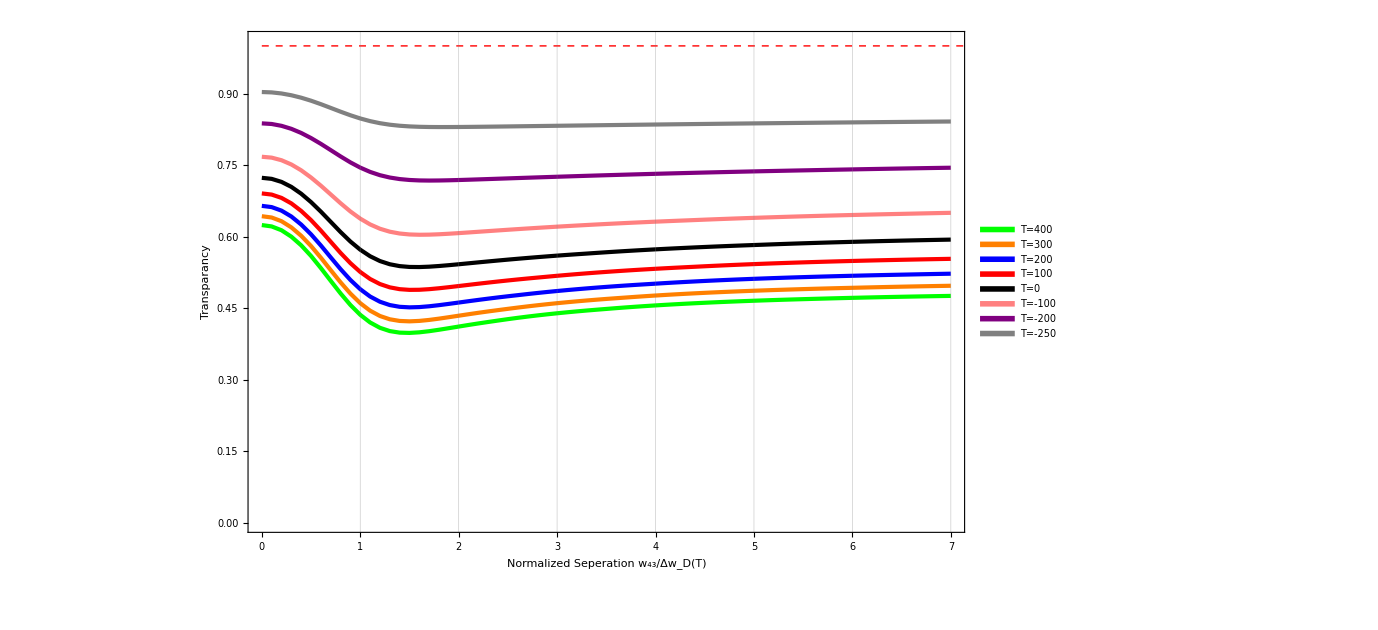

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw3γ5[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

γ=1.438MHZ

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
γ=1.438;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[T];
Tvw4γ14[T]={};Tvw3γ14[T]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw4γ14[T]=Append[Tvw4γ14[T],{i,1-EIT1/ABS1}];
Tvw3γ14[T]=Append[Tvw3γ14[T],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{T,{400,300,200,100,0,-100,-200,-250}}]
]
```

400

300

200

100

0

-100

-200

-250

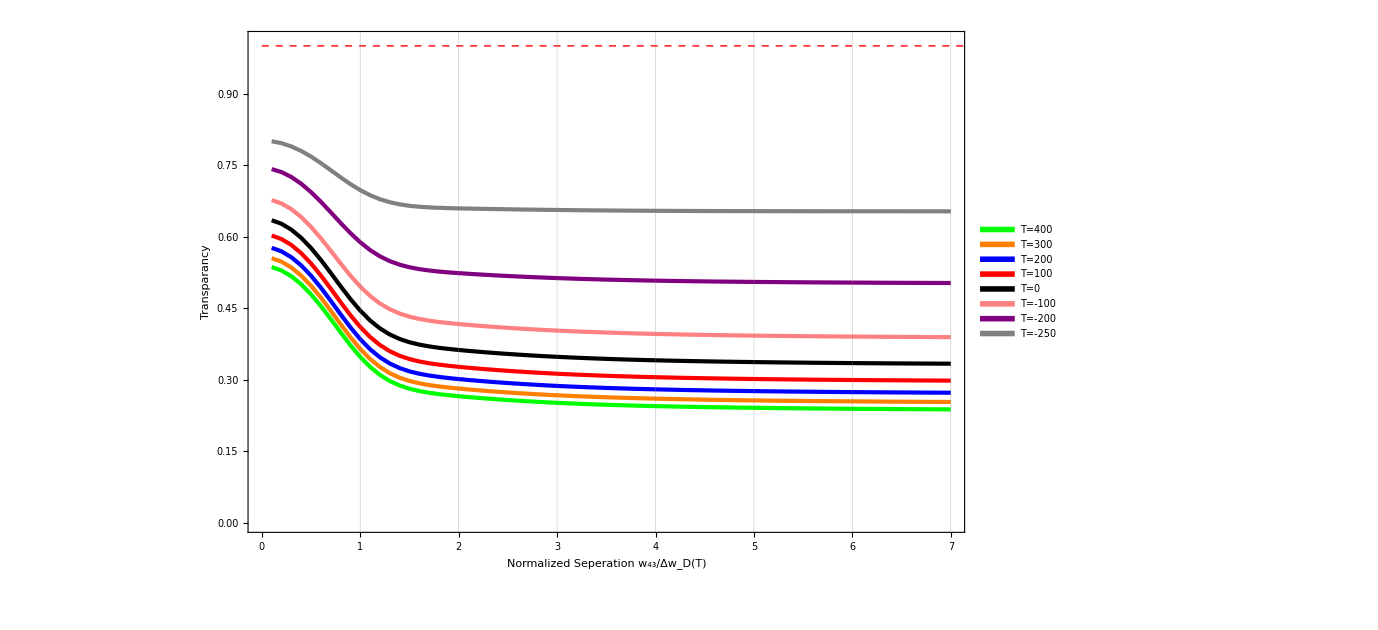

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw4γ14[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

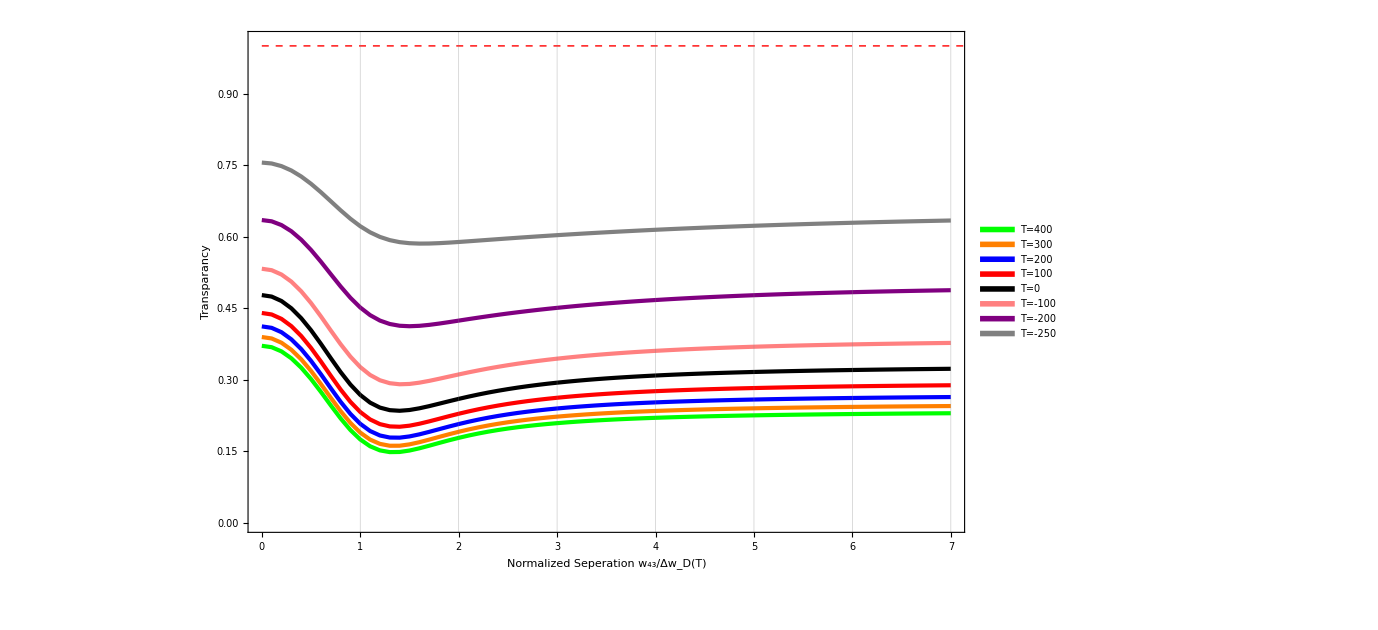

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["T=400",Green],Style["T=300",Orange],Style["T=200",Blue],Style["T=100",Red],Style["T=0",Black],Style["T=-100",Pink],Style["T=-200",Purple],Style["T=-250",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw3γ14[T],{T,{400,300,200,100,0,-100,-200,-250}}],PlotLegends->Placed[legend,{Right,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},{0,1.01}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

## TvS vs Decoh

P=1

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=1;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41p1[γ]={};Tvw31p1[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41p1[γ]=Append[Tvw41p1[γ],{i,1-EIT1/ABS1}];
Tvw31p1[γ]=Append[Tvw31p1[γ],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1

1.1

1.2

1.3

1.4

1.5

P=5

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=5;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41p5[γ]={};Tvw31p5[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41p5[γ]=Append[Tvw41p5[γ],{i,1-EIT1/ABS1}];
Tvw31p5[γ]=Append[Tvw31p5[γ],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1

1.1

1.2

1.3

1.4

1.5

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw41p5[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw31p5[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

P=15.8

```mathematica
5.750056*0.25
5.750056*0.10
5.750056*0.05
5.750056*0.01
```

1.43751

0.575006

0.287503

0.0575006

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41[γ]={};Tvw31[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41[γ]=Append[Tvw41[γ],{i,1-EIT1/ABS1}];
Tvw31[γ]=Append[Tvw31[γ],{i,1-EIT/ABS}];
,{i,0.01,7,0.1}]
,{γ,{0,0.0575,0.287503,0.575006,1.43751}}]
]
```

0

0.0575

0.287503

0.575006

1.43751

```mathematica
5.750056*0.25
5.750056*0.10
5.750056*0.05
5.750056*0.01
```

0.0575

```mathematica
0.01,0.05,0.1,0.25
```

-Graphics-

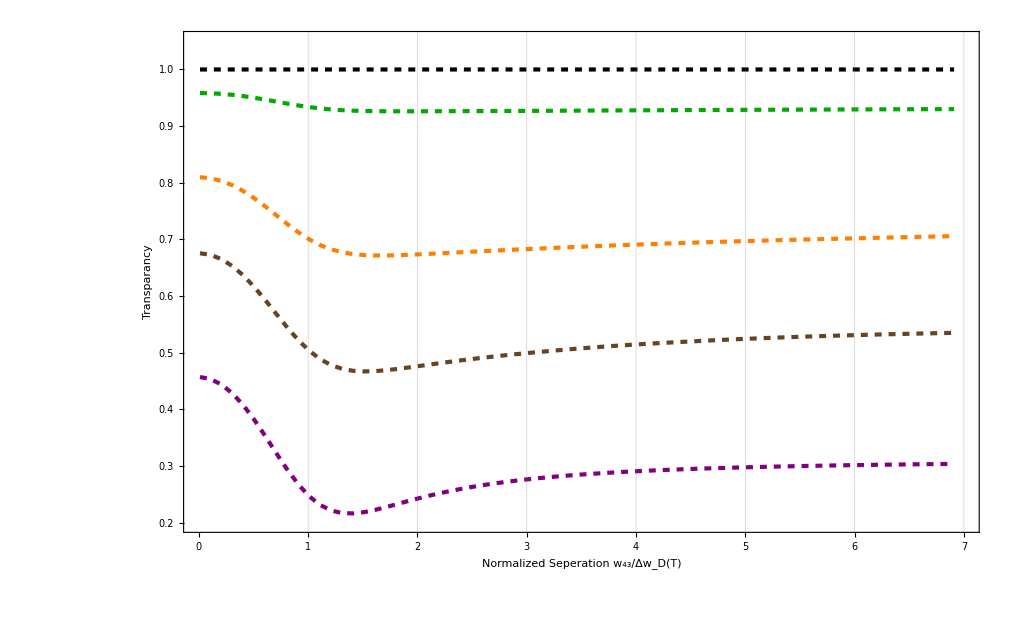

```mathematica
legend=
LineLegend[Thread[Directive[{Black,Darker[Green],Orange,Darker[Brown],Purple},AbsoluteThickness[10]]],{Style["γ=0",Black],Style["0.01γ",Darker[Green]],Style["0.05γ",Orange],Style["0.1γ",Darker[Brown]],Style["0.25γ",Purple]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM1=ListPlot[Table[Tvw41[γ],{γ,{0,0.0575,0.287503,0.575006,1.43751}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Purple}}
,PlotRange->{{0,7},{0.2,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
MMM2=ListPlot[Table[Tvw31[γ],{γ,{0,0.0575,0.287503,0.575006,1.43751}}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Darker[Green],Dashed},{AbsoluteThickness[3],Orange,Dashed},{AbsoluteThickness[3],Darker[Brown]
,Dashed},{AbsoluteThickness[3],Purple,Dashed}}
,PlotRange->{{0,7},{0.2,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
MMMp15=Show[MMM2,MMM1]
```

-Graphics-

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\Final-Paper Figure"]
Export["Figure9Combinedf2.eps",MMMp15]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\Final-Paper Figure

Figure9Combinedf2.eps

```mathematica
Lev3xsingleDoppTestscSep[T_,P_,diam_,gam_,delt_,k_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[2/27]*2.537717 10^-29;
d41=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(0*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

{Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]],Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]],Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}[[k]]

]
```

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=1.43751;
Module[{list,list1,EIT,ABS},
Tvw31s[γ,1]={};Tvw31s[γ,2]={};Tvw31s[γ,3]={};
Do[
list=Lev3xsingleDoppTestscSep[T,p/1000,1/1000,γ*10^6,0,k];
list1=Lev3xsingleDoppTestscSep[T,0/1000,1/1000,γ*10^6,0,k];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31s[γ,k]=Append[Tvw31s[γ,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.1},{k,{1,2,3}}]

]
```

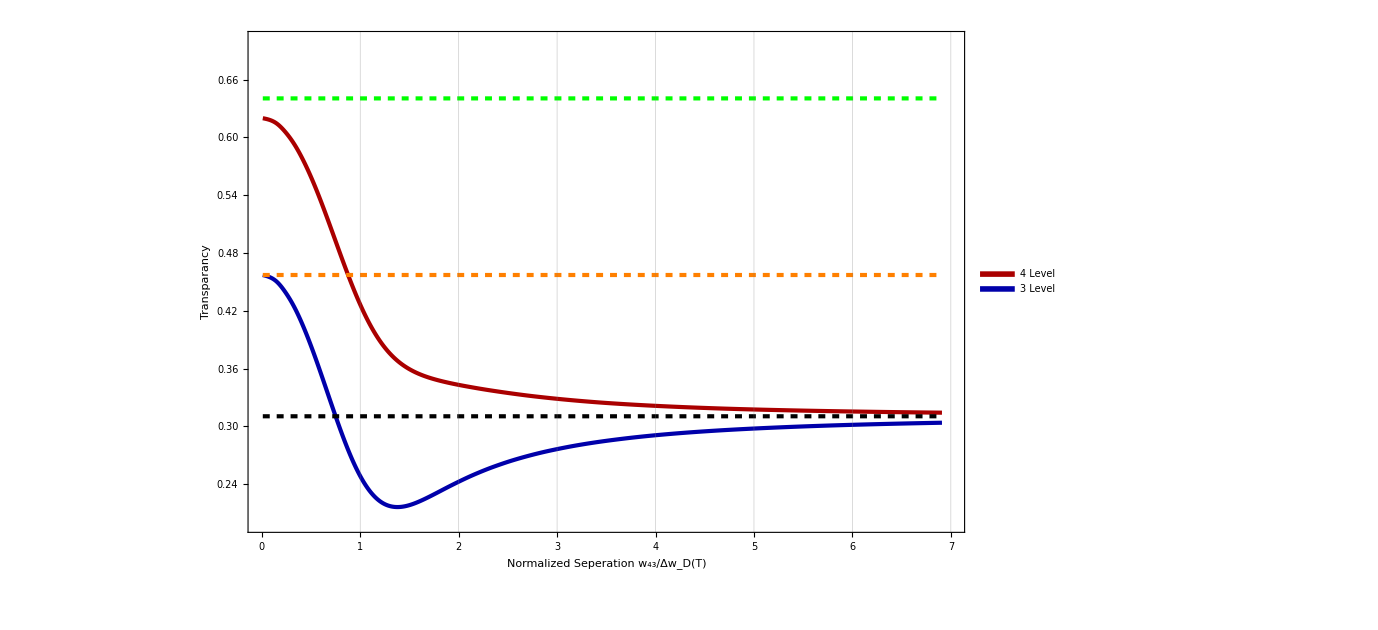

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ025=ListLinePlot[{Tvw41[1.43751],Tvw31[1.43751],Tvw31s[1.43751,1],Tvw31s[1.43751,2],Tvw31s[1.43751,3]},ImageSize->1020, InterpolationOrder->4,PlotLegends->Placed[legend,{0.8,0.7}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0.2,0.7}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
Export["Figure9Combinedf3.eps",MMMp15γ025]
```

Figure9Combinedf3.eps

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.0575;
Module[{list,list1,EIT,ABS},
Tvw31s[γ,1]={};Tvw31s[γ,2]={};Tvw31s[γ,3]={};
Do[
list=Lev3xsingleDoppTestscSep[T,p/1000,1/1000,γ*10^6,0,k];
list1=Lev3xsingleDoppTestscSep[T,0/1000,1/1000,γ*10^6,0,k];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31s[γ,k]=Append[Tvw31s[γ,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.1},{k,{1,2,3}}]

]
```

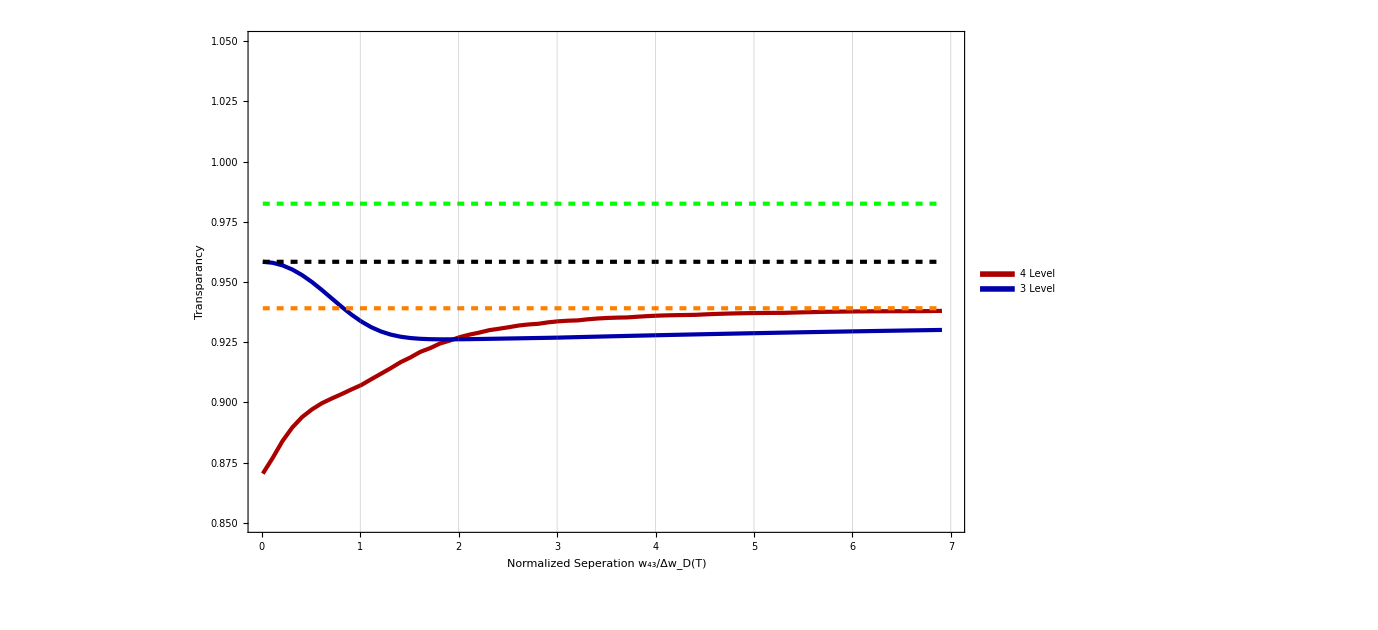

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMMp15γ005=ListLinePlot[{Tvw41[0.0575],Tvw31[0.0575],Tvw31s[0.0575,1],Tvw31s[0.0575,2],Tvw31s[0.0575,3]},ImageSize->1020, InterpolationOrder->1,PlotLegends->Placed[legend,{0.8,0.81}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Orange,Dashed},{AbsoluteThickness[3],Black,Dashed}}
,PlotRange->{{0,7},{0.85,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
```

```mathematica
SetDirectory["D:\\Qsync\\PersonalFolders\\Saesun\\Papers\\Paper\\Final-Paper Figure"]
Export["Figure9Combinedf4.eps",MMMp15γ005]
```

D:\Qsync\PersonalFolders\Saesun\Papers\Paper\Final-Paper Figure

Figure9Combinedf4.eps

P=50

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=50;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41p50[γ]={};Tvw31p50[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41p50[γ]=Append[Tvw41p50[γ],{i,1-EIT1/ABS1}];
Tvw31p50[γ]=Append[Tvw31p50[γ],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1

1.1

1.2

1.3

1.4

1.5

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw41p50[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray,Darker[Green],Darker[Orange],Darker[Blue],Darker[Red],Darker[Gray],Darker[Pink],Darker[Purple],Darker[Yellow]},AbsoluteThickness[10]]],{Style["γ=0",Green],Style["0.1",Orange],Style["0.2",Blue],Style["0.3",Red],Style["0.4",Black],Style["0.5",Pink],Style["0.6",Purple],Style["0.7",Gray],Style["0.8",Darker[Green]],Style["0.9",Darker[Orange]],Style["1.0",Darker[Blue]],Style["1.1",Darker[Red]],Style["1.2",Darker[Gray]],Style["1.3",Darker[Pink]],Style["1.4",Darker[Purple]],Style["1.5",Darker[Yellow]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw31p50[γ],{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Darker[Green]},{AbsoluteThickness[3],Darker[Orange]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Gray]},{AbsoluteThickness[3],Darker[Pink]},{AbsoluteThickness[3],Darker[Purple]},{AbsoluteThickness[3],Darker[Yellow]}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

P=100

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=100;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[γ];
Tvw41[γ]={};Tvw31[γ]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41[γ]=Append[Tvw41[γ],{i,1-EIT1/ABS1}];
Tvw31[γ]=Append[Tvw31[γ],{i,1-EIT/ABS}];
,{i,0,7,0.05}]
,{γ,{0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1,1.2,1.3,1.4,1.5}}]
]
```

0

0.1

0.2

0.3

0.4

0.5

$Aborted

```mathematica
Effect of two close excited state
```

## TvS vs Power

γ=0

```mathematica
Off[Power::infy];Off[Infinity::indet];Off[General::ovfl];
γ=0;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ0[p]={};Tvw32γ0[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ0[p]=Append[Tvw42γ0[p],{i,1-EIT1/ABS1}];
Tvw32γ0[p]=Append[Tvw32γ0[p],{i,1-EIT/ABS}];
,{i,0,5,0.25}]
,{p,{0,5,10,15,20}}]
]
```

0

5

10

15

20

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Red]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ0[p],{p,{0,5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Red]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ0[p],{p,{0,5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=0.1

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
γ=0.1;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ5[p]={};Tvw32γ5[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ5[p]=Append[Tvw42γ5[p],{i,1-EIT1/ABS1}];
Tvw32γ5[p]=Append[Tvw32γ5[p],{i,1-EIT/ABS}];
,{i,0,5,0.25}]
,{p,{5,10,15,20}}]
]
```

5

10

15

20

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ5[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.6,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ5[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.6,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=0.5

```mathematica
Clear[Tvw4,Tvw3]
Off[Power::infy];Off[Infinity::indet];
γ=0.5;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ1[p]={};Tvw32γ1[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ1[p]=Append[Tvw42γ1[p],{i,1-EIT1/ABS1}];
Tvw32γ1[p]=Append[Tvw32γ1[p],{i,1-EIT/ABS}];
,{i,0,5,0.25}]
,{p,{5,10,15,20}}]
]
```

5

10

15

20

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ1[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.1,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["5",Orange],Style["10",Blue],Style["15",Red],Style["20",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ1[p],{p,{5,10,15,20}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,5},{0.1,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=1

```mathematica
Off[Power::infy];Off[Infinity::indet];
γ=1;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42γ14[p]={};Tvw32γ14[p]={};
Do[
list=Lev3DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestscp[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestscp[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42γ14[p]=Append[Tvw42γ14[p],{i,1-EIT1/ABS1}];
Tvw32γ14[p]=Append[Tvw32γ14[p],{i,1-EIT/ABS}];
,{i,0,7,0.1}]
,{p,{0,10,50,100}}]
]
```

0

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1⟧ cannot be used as a part specification.

1

5

10

20

50

$Aborted

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["1",Orange],Style["5",Blue],Style["10",Red],Style["20",Black],Style["50",Pink],Style["100",Purple],Style["200",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw42γ14[p],{p,{0,1,5,10,20,50,100,200}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

```mathematica
legend=
LineLegend[Thread[Directive[{Green,Orange,Blue,Red,Black,Pink,Purple,Gray},AbsoluteThickness[10]]],{Style["P=0",Green],Style["1",Orange],Style["5",Blue],Style["10",Red],Style["20",Black],Style["50",Pink],Style["100",Purple],Style["200",Gray]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM2=ListPlot[Table[Tvw32γ14[p],{p,{0,1,5,10,20,50,100,200}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Green},{AbsoluteThickness[3],Orange},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Red},{AbsoluteThickness[3],Black},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Gray}}
,PlotRange->{{0,7},All},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]},Epilog->{Dashed,Red,Line[{{0,1},{7.90,1}}]}]
```

-Graphics-

γ=5

```mathematica
Off[Power::infy];Off[Infinity::indet];
γ=5;
T=50;
Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[p];
Tvw42[p]={};Tvw32[p]={};
Do[
list=Lev3DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list1=Lev3DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list3=Lev4DoppTestsc[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];
list4=Lev4DoppTestsc[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw42[p]=Append[Tvw42[p],{i,1-EIT1/ABS1}];
Tvw32[p]=Append[Tvw32[p],{i,1-EIT/ABS}];
,{i,0,7,0.05}]
,{p,{0,1,5,10,20,50,100,200}}]
]
```

# Investigate

```mathematica
Lev4DoppTestscpd[T_,P_,diam_,gam_,delt_,ab_,w_,diff_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;

d31=Sqrt[(4.5-diff)/27]*2.537717 10^-29;
d41=Sqrt[(4.5+diff)/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 


(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])


]
```

```mathematica
Lev3DoppTestscpd[T_,P_,diam_,gam_,delt_,ab_,w_,diff_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[(4.5-diff)/27]*2.537717 10^-29;
d41=Sqrt[(4.5+diff)/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(w*10^6)  ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])

]
```

```mathematica
Lev3xsingleDoppTestscSepd[T_,P_,diam_,gam_,delt_,k_,diff_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.001,0.002,0.00001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d32=Sqrt[5/27]*2.537717 10^-29;
d42=Sqrt[4/27]*2.537717 10^-29;
d31=Sqrt[(4.5-diff)/27]*2.537717 10^-29;
d41=Sqrt[(4.5+diff)/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(0*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

{Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]],Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]],Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}[[k]]

]
```

## γ12=0.5MHZ

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.5;

Module[{list,list1,list3,list4,EIT,ABS,EIT1,ABS1},
Do[
Print[d];
Tvw41γd[d]={};Tvw31γd[d]={};
Do[
list=Lev3DoppTestscpd[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];
list1=Lev3DoppTestscpd[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];
list3=Lev4DoppTestscpd[T,p/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];
list4=Lev4DoppTestscpd[T,0/1000,1/1000,γ*10^6,0,0,i*Rbpress[T][[2]]*10^-6,d];

EIT=Min[DeleteCases[list,Indeterminate]];
EIT1=Min[DeleteCases[list3,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];
ABS1=list4[[Position[list3,EIT1][[1]]]][[1]];

Tvw41γd[d]=Append[Tvw41γd[d],{i,1-EIT1/ABS1}];
Tvw31γd[d]=Append[Tvw31γd[d],{i,1-EIT/ABS}];
,{i,0.01,7,0.25}]
,{d,{0,1,2,3,4}}]

]
```

0

1

2

3

4

```mathematica
legend=
LineLegend[Thread[Directive[{Darker[Brown],Purple,Pink,Gray,Black},AbsoluteThickness[10]]],{Style["d=0",Darker[Brown]],Style["d=1",Purple],Style["d=2",Pink],Style["d=3",Gray],Style["d=4",Black]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->20}];
MMM1=ListPlot[Table[Tvw41γd[d],{d,{0,1,2,3,4}}],PlotLegends->Placed[legend,{1.,Center}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Black}}
,PlotRange->{{0,7},{0.2,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}];
MMM2=ListPlot[Table[Tvw31γd[d],{d,{0,1,2,3,4}}],ImageSize->1020,Joined->True,
PlotStyle-> {{AbsoluteThickness[3],Darker[Brown]},{AbsoluteThickness[3],Purple},{AbsoluteThickness[3],Pink},{AbsoluteThickness[3],Gray},{AbsoluteThickness[3],Black}}
,PlotRange->{{0,7},{0.2,1.05}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}];
Show[MMM1,MMM2]
```

-Graphics-

```mathematica
Off[Power::infy];Off[Infinity::indet];
p=15.865;
T=50;
γ=0.5;

Module[{list,list1,EIT,ABS},
Do[
Tvw31sd[d,1]={};Tvw31sd[d,2]={};Tvw31sd[d,3]={};
Do[
list=Lev3xsingleDoppTestscSepd[T,p/1000,1/1000,γ*10^6,0,k,d];
list1=Lev3xsingleDoppTestscSepd[T,0/1000,1/1000,γ*10^6,0,k,d];

EIT=Min[DeleteCases[list,Indeterminate]];

ABS=list1[[Position[list,EIT][[1]]]][[1]];

Tvw31sd[d,k]=Append[Tvw31sd[d,k],{i,1-EIT/ABS}];
,{i,0.01,7,0.5},{k,{1,2,3}}]
,{d,{0,1,2,3,4}}]
]
```

```mathematica
Manipulate[
legend=
LineLegend[Thread[Directive[{Darker[Red],Darker[Blue]},AbsoluteThickness[10]]],{Style["4 Level",Darker[Red]],Style["3 Level",Darker[Blue]]},LegendMarkerSize->Large,LegendFunction->"Frame",LabelStyle->{FontSize->50}];
MMM1=ListLinePlot[{Tvw41γd[d],Tvw31γd[d],Tvw31sd[d,1],Tvw31sd[d,2],Tvw31sd[d,3]},ImageSize->1020, InterpolationOrder->4,PlotLegends->Placed[legend,{0.8,0.7}],
PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Darker[Blue]},{AbsoluteThickness[3],Green,Dashed},{AbsoluteThickness[3],Black,Dashed},{AbsoluteThickness[3],Orange,Dashed}}
,PlotRange->{{0,7},{0,1}},Frame->True,Axes->False,FrameTicks->True,FrameTicksStyle->Directive[40],GridLines->{{1,2,3,4,5,6,7,8},{}},FrameLabel->{Style["Normalized Seperation w_43/Δw_D(T)",50,Black],Style["Transparancy ",50,Black]}]
,{d,0,4,1}]
```

## γ12=1.4MHZ